# 1. Simple SIR Model

This is the first simple SIR Model to model a zombie apocalypse.
- Susceptible (S): The human population who are healthy but vulnerable to being attacked by zombies.
- Infected (I): The zombie population who are able to attack humans and therefore expand the zombie population.
- Removed (R): The combined population of dead humans and zombies which have no influence on the human or zombie populations.
- β: The rate at which zombies infect humans.
- α: The rate at which zombies are neutralized or removed from the system.

## Parameters

```mathematica
beta = 0.5; (*Infection rate *)
alpha = 0; (* Zombie removal rate, set the 0 initially under the assumption that the zombies can't die *)
horizon = 7; (* The number of days to simulate over *)
```

## Initial Conditions

```mathematica
S0 = 100; (* Initial population of humans *)
I0 = 1; (* Initial population of zombies *)
R0 = 0; (* Initial removed population *)
```

## Differential Equations

Set up and solve the differential equations using NDSolve.

```mathematica
zModel = NDSolve[
	{
	S'[t] == -beta * S[t] * Z[t],
	Z'[t] == beta * S[t] * Z[t] - alpha * Z[t],
	R'[t] == alpha * Z[t],
	S[0] == S0,
	Z[0] == I0,
	R[0] == R0
	},
	{S, Z, R}, {t, 0, horizon}
];
```

## Plotting

Standard time-series plot of all three populations.

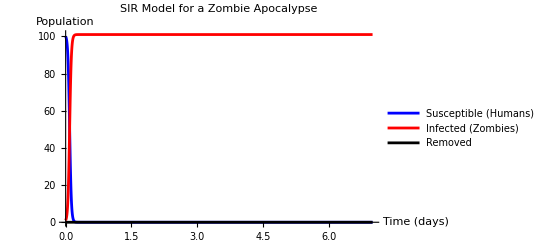

```mathematica
Plot[
 Evaluate[{S[t], Z[t], R[t]} /. zModel],
 {t, 0, horizon},
 PlotLegends -> {"Susceptible (Humans)", "Infected (Zombies)", "Removed"},
 PlotStyle -> {Blue, Red, Black},
 AxesLabel -> {"Time (days)", "Population"},
 PlotLabel -> "SIR Model for a Zombie Apocalypse"
]
```